# Many Elements (Entropies from Kraftmakher)

```mathematica
(*Sexp= 3.19;
Tmelt=1235;
H[T_]=1.125;*)
(*
S=a*T;
dH/dT = T dS/dT
-> dH/dT = T a   (1)
-> int(1) -> H = 0.5 a T^2  + inegrationskonstante 
-> integrationskonstante ist H0

*)
elements={"CS","Rb","K","Na","In","Sn","Pb","Zn","Sb","Al","Au","Cu","Ni","Ti","Pt","Zr","Cr","Rh","Nb","Mo","Ta","W"};
cohesiveenergy={};
melting={302,312,336,371,430,505,600,693,903,933,1337,1358,1728,1940,2041,2125,2180,2237,2750,2896,3290,3695};
entropy={4.95,5.5,2.55,3.1,3.95,3.8,2.3,4.1,7.8,4.5,3.15,3.7,5.4,5.15,4.5,4.6,6.3,5.25,4.15,5.7,5.45,6.5};
entropy=entropy/1;
enthalpycplin={0.28,0.31,0.23,0.255,0.425,0.455,0.435,0.61,1.13,0.87,1.0,1.05,1.4,1.55,1.6,1.75,1.68,1.9,2.04,2.24,2.9,3.15};
{elements//Length,melting//Length,entropy//Length,enthalpycplin//Length}
```

{22,22,22,22}

```mathematica
correctionlist={};
correctionovertmeltlist={};
Do[
kBineVoverK=0.00008616135;
Sexp=4;(*kB at Tmelt*) (*Hier veraendert nur die Entropie die correction*)
Tmelt=1358;(*K*)
element=elements[[i]];
H[T_]:=0;
Sexp=entropy[[i]];
Tmelt=melting[[i]];
Sold[T_]:=Sexp;
Snew[T_]:=Sexp  T/Tmelt;
Gold[T_]:=H[T]-T Sold[T]kBineVoverK;
Gnew[T_]:=H[T]+T Snew[T]kBineVoverK 0.5-T Snew[T]kBineVoverK;
correction=Gold[Tmelt]-Gnew[Tmelt];
AppendTo[correctionlist,{Tmelt,-correction}];
AppendTo[correctionovertmeltlist,{Tmelt,-correction/Tmelt}];
Gnewc[T_]:=correction + Gnew[T];
(*
Sold[T_]:=S[T];
Snew[T_]:=S[T]  T/Tmelt;
Gold[T_]:=H[T]-T Sold[T]kBineVoverK;
Gnew[T_]:=H[T]+T Snew[T]kBineVoverK 0.5-T Snew[T]kBineVoverK;
correction=Gold[Tmelt]-Gnew[Tmelt];
Gnewc[T_]:=correction + Gnew[T];
*)


Plot[{Sold[T],Snew[T]},{T,0,Tmelt}];
Plot[{Gold[T],Gnewc[T]},{T,0,Tmelt}];
Print[i,"--",element,"    Tmelt: ",Tmelt,"     S: ",Sexp,"    correction:",correction, "----",(correction/enthalpycplin[[i]])*100,"%","    H: ",enthalpycplin[[i]]]
,{i,1,elements//Length}]
```

1--CS    Tmelt: 302     S: 4.95    correction:-0.0644013-----23.0005%    H: 0.28

2--Rb    Tmelt: 312     S: 5.5    correction:-0.0739264-----23.8472%    H: 0.31

3--K    Tmelt: 336     S: 2.55    correction:-0.0369115-----16.0485%    H: 0.23

4--Na    Tmelt: 371     S: 3.1    correction:-0.0495471-----19.4302%    H: 0.255

5--In    Tmelt: 430     S: 3.95    correction:-0.0731725-----17.2171%    H: 0.425

6--Sn    Tmelt: 505     S: 3.8    correction:-0.0826718-----18.1696%    H: 0.455

7--Pb    Tmelt: 600     S: 2.3    correction:-0.0594513-----13.667%    H: 0.435

8--Zn    Tmelt: 693     S: 4.1    correction:-0.122405-----20.0664%    H: 0.61

9--Sb    Tmelt: 903     S: 7.8    correction:-0.303434-----26.8526%    H: 1.13

10--Al    Tmelt: 933     S: 4.5    correction:-0.180874-----20.7901%    H: 0.87

11--Au    Tmelt: 1337     S: 3.15    correction:-0.181436-----18.1436%    H: 1.

12--Cu    Tmelt: 1358     S: 3.7    correction:-0.216463-----20.6155%    H: 1.05

13--Ni    Tmelt: 1728     S: 5.4    correction:-0.401994-----28.7139%    H: 1.4

14--Ti    Tmelt: 1940     S: 5.15    correction:-0.430419-----27.769%    H: 1.55

15--Pt    Tmelt: 2041     S: 4.5    correction:-0.395674-----24.7297%    H: 1.6

16--Zr    Tmelt: 2125     S: 4.6    correction:-0.421114-----24.0636%    H: 1.75

17--Cr    Tmelt: 2180     S: 6.3    correction:-0.59167-----35.2185%    H: 1.68

18--Rh    Tmelt: 2237     S: 5.25    correction:-0.50595-----26.629%    H: 1.9

19--Nb    Tmelt: 2750     S: 4.15    correction:-0.491658-----24.1009%    H: 2.04

20--Mo    Tmelt: 2896     S: 5.7    correction:-0.711141-----31.7474%    H: 2.24

21--Ta    Tmelt: 3290     S: 5.45    correction:-0.772458-----26.6365%    H: 2.9

22--W    Tmelt: 3695     S: 6.5    correction:-1.03469-----32.8473%    H: 3.15

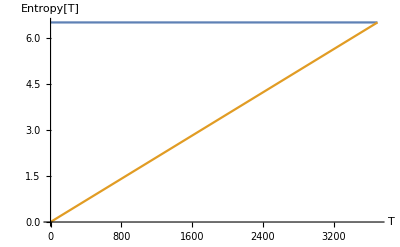
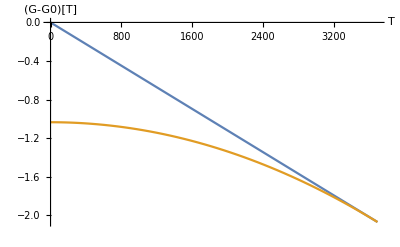
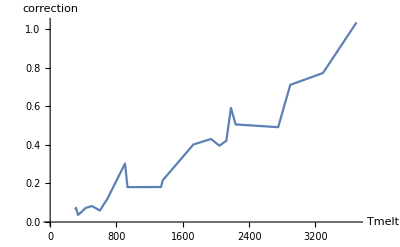
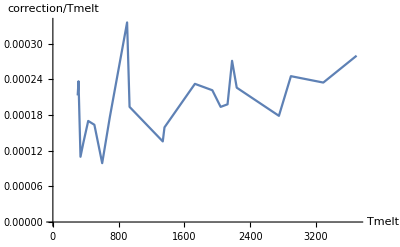
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,/Users/glensk/Dropbox/Albert/google_drive/Glensk/KMC-Tutorial/scripts/}

```mathematica
{
Plot[{Sold[T],Snew[T]},{T,0,Tmelt},AxesLabel->{"T","Entropy[T]"}],
Plot[{Gold[T],Gnewc[T]},{T,0,Tmelt},AxesLabel->{"T","(G-G0)[T]"}],
ListLinePlot[correctionlist,AxesLabel->{"Tmelt","correction"}],
ListLinePlot[correctionovertmeltlist,AxesLabel->{"Tmelt","correction/Tmelt"}],
NotebookDirectory[]
}
```

```mathematica
list=Table[{T,Gnew[T]},{T,0,Tmelt}];
Export["linSmodel.dat",list,"Table"];
```

# Get G with old and “new” entropy model

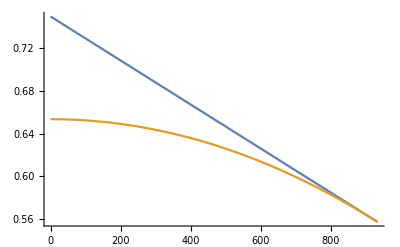

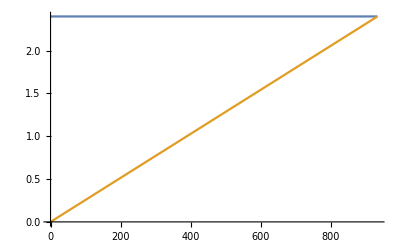

1.53873×10^-11

0.000988129

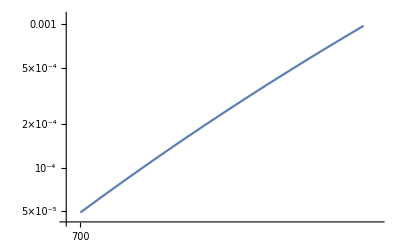

0.557068

Quenching at 560Celcius == 833.15K

nvacnew[873]0.000324759

nvacold[873]0.000319799

nvacnew[934]0.000988129

nvacold[934]0.000988127

nvacnew[300]1.53873×10^-11

nvacold[300]2.76127×10^-12

nvcaolddefine[873,0.75,2.4]0.000515227

nvcaolddefine[873,0.657,1.5]0.000721259

--------

nvcaold[873]

0.000515227

0.000209476

0.000517967

```mathematica
kBineVoverK=0.00008616135;
H[T_]=0.75;(*eV*)
S[T_]=2.4;(*kb*)
Tmelt=933;(*K*)
Sold[T_]:=S[T];
Snew[T_]:=S[T]  T/Tmelt;
Gold[T_]:=H[T]-T Sold[T]kBineVoverK;
Gnew[T_]:=H[T]+T Snew[T]kBineVoverK 0.5-T Snew[T]kBineVoverK;
correction=Gold[Tmelt]-Gnew[Tmelt];
Gnewc[T_]:=correction + Gnew[T];


Plot[{Gold[T],Gnewc[T]},{T,0,Tmelt}]
Plot[{Sold[T],Snew[T]},{T,0,Tmelt}]
nvacnew [T_]:=Exp[- Gnewc[T]/(T kBineVoverK)]
nvacold[T_]:=Exp[-(H[T]-T Sold[T] kBineVoverK)/(T kBineVoverK)]
nvcaolddefine[T_,H_,S_]:=Exp[-(H-T S kBineVoverK)/(T kBineVoverK)]
nvacnew[300]
nvacnew[934]
LogLogPlot[{nvacnew[T]},{T,700,Tmelt}]
Gnewc[933]
Print["Quenching at 560Celcius == 833.15K"];
TM=934;
TQ=833.15;
RT=300;
Print["nvacnew[873]",nvacnew[TQ]]
Print["nvacold[873]",nvacold[TQ]]
Print["nvacnew[934]",nvacnew[TM]]
Print["nvacold[934]",nvacold[TM]]
Print["nvacnew[300]",nvacnew[RT]]
Print["nvacold[300]",nvacold[RT]]
Print["nvcaolddefine[873,0.75,2.4]",nvcaolddefine[873,0.75,2.4]]
Print["nvcaolddefine[873,0.657,1.5]",nvcaolddefine[873,0.657,1.5]]
Print["--------"]
nvcaold[873]
nvcaolddefine[873,0.75,2.4]
nvcaolddefine[873,0.75,1.5]
nvacnew[873]
```

```mathematica
Directory[]
```

/Users/glensk

```mathematica
Directory[]
gold=Table[{T,Gold[T]},{T,0,Tmelt}];
gnewc=Table[{T,Gnewc[T]},{T,0,Tmelt}];
gold[[-1]]
factor=1000;
gold={gold[[1;;-1,1]],gold[[1;;-1,2]]*factor}//Transpose;
gnewc={gnewc[[1;;-1,1]],gnewc[[1;;-1,2]]*factor}//Transpose;
golda=AppendTo[gold,{}]; (*to get rid of xmgrace import problem, append newline*)
gnewca=AppendTo[gnewc,{}];(*to get rid of xmgrace import problem, append newline*)
Export["newSmodel4.5.dat",gnewc,"Table"];
Export["oldSmodel4.5.dat",gold,"Table"];
```

/Users/glensk

{933,0.557068}

# Mono- Divacancy Picture

c1 @ Tmelt: 0.000691206      c2 @ Tmelt: 0.0001174    ceff @ Tmelt: 0.000926007

Geff @ Tmelt: 0.562086

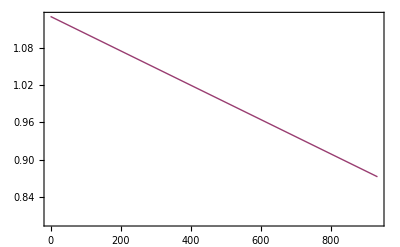
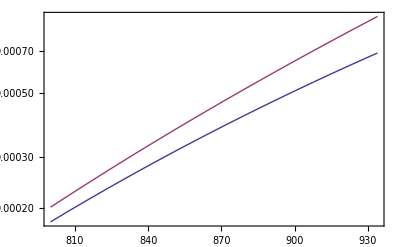
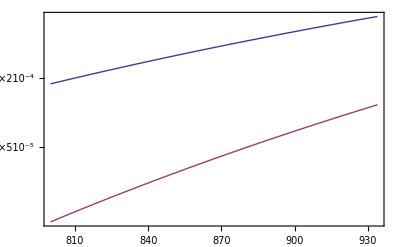
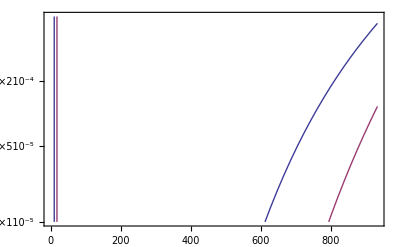
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Export MonoDivakData

Exportet /Users/glensk/Dropbox/proj/results_/__2013_vacancies/

```mathematica
(* values see Neumann 1999*)
H1[T_]=1.03;(*eV*)
S1[T_]=1.08;(*kb*)
H2[T_]=1.826;(*eV*)
S2[T_]=5;(*kb*)
Tmelt=1358;(*K*)


H1[T_]=0.65;(*eV*)
S1[T_]=0.8;(*kb*)
H2[T_]=1.13;(*eV*)
S2[T_]=3.2;(*kb*)
Tmelt=934;(*K*)
(*
H2[T_]=2.15;(*eV*)
S2[T_]=6.7;(*kb*)
*)

kBineVoverK=0.00008616135;
Sold1[T_]:=S1[T];
Gold1[T_]:=H1[T]-T Sold1[T]kBineVoverK;
Sold2[T_]:=S2[T];
Gold2[T_]:=H2[T]-T Sold2[T]kBineVoverK;


c1[T_]:=1Exp[-Gold1[T]/(kBineVoverK T)];(*factor 1 comes from configurational entroy of monovak!*) 
c2[T_]:=6Exp[-Gold2[T]/(kBineVoverK T)]; (*factor 6 comes from configurational entroy of divak!*) 
ceff[T_]:=c1[T]+2c2[T];
Geff[T_]:=-kBineVoverK T Log[ceff[T]];


Print["c1 @ Tmelt: ",c1[Tmelt],"      c2 @ Tmelt: ",c2[Tmelt], "    ceff @ Tmelt: ",ceff[Tmelt]];
Print["Geff @ Tmelt: ",Geff[Tmelt]];

(*
Geff[T_]:=Log[ceff[T] kBineVoverK T (-1)];
ceff[T_]:=c1[T]+2 c2[T];
*)
{Plot[{Gold1[T],Gold2[T],Geff[T]},{T,0,Tmelt},Frame-> True,PlotRange->{{0,Tmelt},{0.85,H1[0]}}],
Plot[{Gold1[T],Gold2[T],Geff[T]},{T,0,Tmelt},Frame-> True,PlotRange->{{0,Tmelt},{0.8,H2[0]}}],
LogPlot[{c1[T],ceff[T]},{T,800,Tmelt},Frame-> True],
LogPlot[{c1[T],c2[T]},{T,800,Tmelt},Frame-> True],
LogPlot[{c1[T],c2[T]},{T,0,Tmelt},Frame-> True,PlotRange->{{0,Tmelt},{0.00001,0.0008}}]
}

Export MonoDivakData
export=True;
If[export,
outGeff=Table[{T,1000Geff[T]},{T,1,Tmelt}][[1;;-1;;10]];
outc1=Table[{Tmelt/T//N,c1[T]},{T,1,Tmelt}][[1;;-1;;10]];
outc2=Table[{Tmelt/T//N,2*c2[T]},{T,1,Tmelt}][[1;;-1;;10]];
outceff=Table[{Tmelt/T//N,ceff[T]},{T,1,Tmelt}][[1;;-1;;10]];
path=NotebookDirectory[];
Export[path<>"MonoDivakNeumann.dat",outGeff,"Table"];
Export[path<>"c1Neumann.dat",outc1,"Table"];
Export[path<>"c2Neumann.dat",outc2,"Table"];
Export[path<>"ceffNeumann.dat",outceff,"Table"];
Print["Exportet "<>path];
];
```